# Lanko s překážkou

```mathematica
ClearAll["Global`*"]
```

## Definice

```mathematica
rho=1;
n=14;
h=1/n;
f[x_]:=0.96-0.25(x-0.5)^2
(*pozn. konstanty jako je g=-1 a k=1 jsme již přímo dosadili*)

Y=Table[Indexed[y,i],{i,1,n-1}];
lamb=Table[Indexed[a,i],{i,1,n-1}];
```

## Výpočet

```mathematica
(*z nějakého důvodu mi nešlo definovat neznámé s indexi (např. a_0), tak bylo nutné tyto členy řešit speciálně*)
Ii=Table[0==(-Y[[i-1]]+2*Y[[i]]-Y[[i+1]])/h^2+Piecewise[{{1+lamb[[i]]+rho*(Y[[i]]-f[i/n]),lamb[[i]]+rho*(Y[[i]]-f[i/n])≤0},{1,lamb[[i]]+rho*(Y[[i]]-f[i/n])>0}}],{i,2,n-2}];
Ii2=Table[0==Piecewise[{{Y[[i]]-f[i/n], lamb[[i]]+rho*(Y[[i]]-f[i/n])≤0},{-lamb[[i]]/rho,lamb[[i]]+rho*(Y[[i]]-f[i/n])>0}}],{i,1,n-1}];
Start={0==(-1+2*Y[[1]]-Y[[2]])/h^2+Piecewise[{{lamb[[1]]+rho*(Y[[1]]-f[1/n]),lamb[[1]]+rho*(Y[[1]]-f[1/n])≤0},{1,lamb[[1]]+rho*(Y[[1]]-f[1/n])>0}}]};
ENd={0==(-Y[[n-2]]+2*Y[[n-1]]-1)/h^2+Piecewise[{{1+lamb[[n-1]]+rho*(Y[[n-1]]-f[(n-1)/n]),lamb[[n-1]]+rho*(Y[[n-1]]-f[(n-1)/n])≤0},{1,lamb[[n-1]]+rho*(Y[[n-1]]-f[(n-1)/n])>0}}]};
```

```mathematica
(*vyřešíme*)
solv=Solve[Join[Start,Ii,ENd,Ii2],Join[Y,lamb]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y1→0.980776,y2→0.966653,y3→0.957633,y4→0.953714,y5→0.954898,y6→0.958724,y7→0.96,y8→0.958724,y9→0.954898,y10→0.953714,y11→0.957633,y12→0.966653,y13→0.980776,a1→0,a2→0,a3→0,a4→0,a5→-0.482,a6→-1.5,a7→-1.5,a8→-1.5,a9→-0.482,a10→0,a11→0,a12→0,a13→0}}

## Vykreslíme

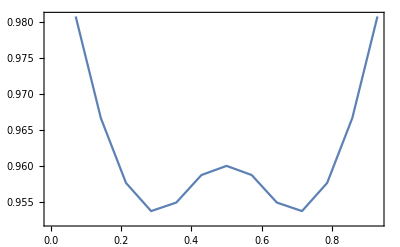

```mathematica
Yres=Table[solv[[1,i,2]],{i,1,n-1}];
Xres=Table[(1/n)i,{i,1,n-1}];
PLot=ListLinePlot[Transpose[{Xres,Yres}],Frame->True,PlotStyle->{black}]
```